```mathematica
RedBlueGreen5[key_]:=Block[{
red=Map[SymbolToLabel[#]&,ListofVars[allGraphs5[key,"colofourrealnull"]]]//Sort,
blue=Map[SymbolToLabel[#]&,ListofVars[allGraphs5[key,"colofour"]]]//Sort,
all=Map[SymbolToLabel[#]&,ListofVars[allGraphs5[0,"colofour"]]]//Sort,
green
},
green=all;
Table[green=Select[green,ToString[#]≠ToString[r]&],{r,red}];
Table[green=Select[green,ToString[#]≠ToString[b]&],{b,blue}];
green=Sort[green];
{red,blue,green}
]
```

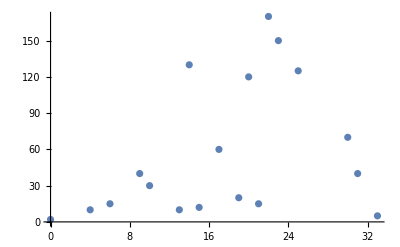

```mathematica
Tally[Table[Length[RedBlueGreen5[k][[3]]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]]//Sort
```

```mathematica
Table[allGraphs5[k,"graph"],{k,Select[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&],Length[RedBlueGreen5[#][[3]]]==6&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[allGraphs5[k,"graph"],{k,Select[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&],Length[RedBlueGreen5[#][[3]]]==0&]}]
```

{-Graphics-,-Graphics-}

```mathematica
Table[allGraphs5[k,"graph"],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&EdgeCount[allGraphs5[#,"graph"]]==2&]}]
```

```mathematica
Table[allGraphs5[k,"graph"],{k,Select[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&],Length[RedBlueGreen5[#][[3]]]==5&]}]
```

```mathematica
Table[allGraphs5[k,"graph"],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&EdgeCount[allGraphs5[#,"graph"]]==1&]}]
```

```mathematica
Table[allGraphs5[k,"graph"],{k,Select[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&],Length[RedBlueGreen5[#][[3]]]==3&]}]
```

```mathematica
Table[allGraphs5[k,"graph"],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&EdgeCount[allGraphs5[#,"graph"]]==3&]}]
```

```mathematica
Table[allGraphs5[k,"graph"],{k,Select[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&],Length[RedBlueGreen5[#][[3]]]==1&]}]
```

```mathematica
Table[allGraphs5[k,"graph"],{k,Select[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&],Length[RedBlueGreen5[#][[3]]]==0&]}]
```

```mathematica
Table[allGraphs5[k,"graph"],{k,Select[Keys[allGraphs5],Length[RedBlueGreen5[#][[3]]]==7&]}]
```

```mathematica
TableForm[Sort[Tally[Table[RedBlueGreen5[k][[3]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]],#1[[2]]#2[[2]]&],TableDepth->2]
```

```mathematica
vals345=Table[{Length[RedBlueGreen5[k][[3]]],Length[RedBlueGreen5[FindComplement[ k,allGraphs5]][[3]]]},{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]
```

{{0,0},{14,4},{22,10},{25,19},{22,33},{23,31},{20,30},{13,31},{10,22},{4,14},{0,0},{4,14},{10,22},{4,14},{10,22},{19,25},{10,22},{4,14},{10,22},{14,25},{6,22},{14,25},{20,30},{14,25},{10,22},{4,14},{6,22},{19,25},{10,22},{14,25},{20,30},{13,31},{10,22},{14,25},{20,30},{14,25},{21,25},{23,31},{20,30},{14,25},{6,22},{4,14},{10,22},{14,25},{10,22},{19,25},{20,30},{14,25},{10,22},{13,31},{21,25},{14,25},{20,30},{23,31},{21,25},{14,25},{10,22},{14,25},{20,30},{13,31},{20,30},{23,31},{20,30},{19,25},{20,30},{23,31},{20,30},{23,31},{30,20},{31,23},{20,30},{19,25},{10,22},{4,14},{10,22},{14,25},{6,22},{14,25},{33,22},{19,25},{10,22},{19,25},{20,22},{9,25},{20,22},{23,23},{20,22},{14,25},{6,22},{9,25},{20,22},{9,25},{14,22},{31,23},{20,30},{14,25},{20,22},{23,23},{14,22},{23,17},{30,20},{23,23},{20,22},{9,25},{6,22},{14,25},{14,22},{9,25},{20,22},{31,23},{20,22},{14,25},{20,30},{23,17},{14,22},{23,23},{22,20},{23,17},{14,22},{9,25},{14,22},{17,23},{9,30},{17,23},{30,20},{23,23},{20,22},{23,23},{22,20},{17,23},{22,20},{25,19},{30,20},{23,23},{20,30},{14,25},{10,22},{4,14},{6,22},{19,25},{10,22},{14,25},{20,22},{14,25},{6,22},{9,25},{20,22},{9,25},{14,22},{31,23},{20,22},{19,25},{10,22},{9,25},{33,22},{19,25},{20,22},{23,23},{20,30},{14,25},{14,22},{31,23},{20,22},{23,17},{22,20},{23,23},{14,22},{9,25},{6,22},{9,25},{20,22},{14,25},{20,22},{17,23},{14,22},{9,25},{9,30},{23,17},{14,22},{17,23},{30,20},{23,17},{20,22},{14,25},{14,22},{31,23},{20,30},{23,23},{22,20},{23,23},{20,22},{17,23},{30,20},{23,23},{22,20},{31,13},{30,20},{23,31},{20,30},{13,31},{10,22},{14,25},{20,30},{14,25},{21,25},{31,23},{20,30},{14,25},{20,22},{23,23},{14,22},{23,17},{30,20},{23,23},{20,30},{14,25},{14,22},{31,23},{20,22},{23,17},{30,20},{23,31},{21,25},{23,17},{30,20},{23,17},{30,9},{25,14},{22,20},{17,23},{9,30},{9,25},{14,22},{17,23},{14,22},{23,17},{25,21},{17,23},{14,22},{17,23},{22,14},{15,15},{22,14},{25,14},{22,14},{17,23},{14,22},{15,15},{25,21},{17,23},{22,14},{25,14},{22,20},{23,17},{22,14},{25,14},{22,14},{25,9},{22,10},{25,19},{22,20},{23,23},{20,30},{14,25},{6,22},{4,14},{10,22},{14,25},{10,22},{19,25},{20,22},{9,25},{6,22},{14,25},{14,22},{9,25},{20,22},{23,23},{14,22},{9,25},{6,22},{9,25},{20,22},{14,25},{20,22},{17,23},{9,30},{9,25},{14,22},{17,23},{14,22},{23,17},{30,20},{31,23},{20,22},{9,25},{10,22},{19,25},{20,22},{19,25},{33,22},{23,23},{14,22},{14,25},{20,30},{23,17},{20,22},{31,23},{30,20},{23,17},{14,22},{14,25},{20,22},{23,23},{20,30},{31,23},{22,20},{17,23},{20,22},{23,23},{22,20},{23,23},{30,20},{25,14},{30,20},{23,31},{20,30},{14,25},{10,22},{13,31},{21,25},{14,25},{20,30},{31,23},{20,22},{14,25},{20,30},{23,17},{14,22},{23,23},{22,20},{17,23},{14,22},{9,25},{9,30},{23,17},{14,22},{17,23},{25,21},{17,23},{14,22},{17,23},{22,14},{15,15},{22,14},{31,13},{30,20},{23,23},{14,22},{14,25},{20,30},{23,17},{20,22},{31,23},{30,20},{23,17},{21,25},{23,31},{30,9},{23,17},{30,20},{25,14},{22,14},{15,15},{14,22},{17,23},{22,14},{17,23},{25,21},{25,14},{22,14},{23,17},{22,20},{25,9},{22,14},{25,14},{22,10},{25,14},{22,20},{23,31},{21,25},{14,25},{10,22},{14,25},{20,30},{13,31},{20,30},{23,17},{14,22},{9,25},{14,22},{17,23},{9,30},{17,23},{30,20},{23,17},{20,22},{14,25},{14,22},{31,23},{20,30},{23,23},{22,14},{17,23},{14,22},{15,15},{25,21},{17,23},{22,14},{25,14},{30,20},{23,17},{14,22},{14,25},{20,22},{23,23},{20,30},{31,23},{22,14},{15,15},{14,22},{17,23},{22,14},{17,23},{25,21},{31,13},{30,9},{23,17},{21,25},{23,17},{30,20},{23,31},{30,20},{25,9},{22,14},{23,17},{22,14},{25,14},{22,20},{25,14},{22,10},{25,19},{22,33},{23,31},{20,30},{19,25},{20,30},{23,31},{20,30},{23,31},{30,20},{23,23},{20,22},{23,23},{22,20},{17,23},{22,20},{25,19},{22,20},{23,23},{20,22},{17,23},{30,20},{23,23},{22,20},{25,14},{22,20},{23,17},{22,14},{25,14},{22,14},{25,9},{22,10},{25,19},{22,20},{17,23},{20,22},{23,23},{22,20},{23,23},{30,20},{25,14},{22,14},{23,17},{22,20},{25,9},{22,14},{25,14},{22,10},{25,9},{22,14},{23,17},{22,14},{25,14},{22,20},{25,14},{22,6},{25,9},{30,9},{25,9},{22,6},{25,9},{22,6},{14,4},{22,10},{25,19},{22,20},{17,23},{9,30},{9,25},{6,22},{4,14},{6,22},{9,25},{6,22},{9,25},{20,22},{14,25},{10,22},{14,25},{14,22},{9,25},{14,22},{17,23},{14,22},{14,25},{10,22},{9,25},{20,22},{14,25},{14,22},{23,23},{20,30},{19,25},{20,22},{23,23},{20,22},{23,17},{22,20},{17,23},{14,22},{9,25},{10,22},{14,25},{14,22},{14,25},{20,22},{23,23},{20,22},{19,25},{20,30},{23,17},{20,22},{23,23},{22,20},{23,17},{20,22},{19,25},{20,22},{23,23},{20,30},{23,23},{30,20},{31,23},{33,22},{31,23},{30,20},{31,23},{30,20},{25,14},{25,21},{17,23},{20,22},{14,25},{10,22},{14,25},{14,22},{9,25},{14,22},{31,23},{20,30},{13,31},{20,30},{17,23},{9,30},{17,23},{22,14},{23,17},{21,25},{14,25},{14,22},{23,17},{14,22},{15,15},{30,20},{23,31},{20,30},{23,23},{22,20},{17,23},{22,14},{25,14},{22,14},{23,17},{14,22},{14,25},{21,25},{15,15},{14,22},{23,17},{30,20},{23,23},{20,30},{23,31},{22,14},{17,23},{22,20},{25,9},{30,9},{23,17},{20,22},{23,17},{22,14},{17,23},{22,14},{31,13},{30,20},{31,23},{30,20},{25,14},{25,21},{25,14},{22,10},{25,14},{22,14},{17,23},{14,22},{14,25},{10,22},{9,25},{20,22},{14,25},{14,22},{23,17},{21,25},{14,25},{14,22},{23,17},{14,22},{15,15},{25,21},{17,23},{20,30},{13,31},{9,30},{31,23},{20,30},{17,23},{22,20},{23,31},{20,30},{17,23},{30,20},{23,23},{22,14},{25,9},{22,14},{15,15},{14,22},{14,25},{14,22},{23,17},{21,25},{23,17},{22,14},{23,17},{20,22},{17,23},{30,9},{23,17},{22,14},{25,14},{22,14},{23,23},{20,30},{17,23},{30,20},{23,31},{22,20},{25,14},{30,20},{31,23},{25,21},{31,13},{30,20},{25,14},{22,10},{25,14},{22,20},{23,23},{20,30},{19,25},{20,22},{23,23},{20,22},{23,17},{30,20},{23,31},{20,30},{23,23},{22,20},{17,23},{22,14},{25,14},{22,20},{23,31},{20,30},{17,23},{30,20},{23,23},{22,14},{25,19},{22,33},{23,31},{22,20},{25,19},{22,20},{25,9},{22,6},{25,9},{22,14},{17,23},{20,22},{23,17},{22,14},{23,17},{30,9},{25,14},{22,20},{23,23},{22,20},{25,9},{22,14},{25,9},{22,6},{25,9},{22,20},{23,23},{22,14},{25,14},{22,20},{25,9},{22,10},{25,19},{30,20},{25,14},{22,10},{25,14},{22,6},{14,4},{22,10},{25,9},{22,14},{17,23},{14,22},{9,25},{10,22},{14,25},{14,22},{14,25},{20,22},{23,17},{14,22},{14,25},{21,25},{15,15},{14,22},{23,17},{22,14},{15,15},{14,22},{14,25},{14,22},{23,17},{21,25},{23,17},{22,14},{17,23},{20,22},{23,17},{22,14},{23,17},{30,9},{25,14},{25,21},{17,23},{9,30},{13,31},{20,30},{17,23},{20,30},{31,23},{22,20},{17,23},{20,30},{23,31},{22,14},{23,23},{30,20},{25,14},{22,14},{17,23},{20,30},{23,23},{22,20},{23,31},{30,20},{25,14},{25,21},{31,23},{30,20},{25,14},{30,20},{31,13},{22,6},{25,14},{22,20},{23,23},{20,22},{19,25},{20,30},{23,17},{20,22},{23,23},{30,20},{23,23},{20,30},{23,31},{22,14},{17,23},{22,20},{25,9},{22,14},{23,17},{20,22},{17,23},{30,9},{23,17},{22,14},{25,14},{22,20},{23,23},{22,20},{25,9},{22,14},{25,9},{22,10},{25,14},{22,20},{17,23},{20,30},{23,31},{22,14},{23,23},{30,20},{25,19},{22,20},{23,31},{22,33},{25,9},{22,20},{25,19},{22,6},{25,9},{22,14},{23,23},{22,20},{25,9},{22,20},{25,14},{22,10},{25,14},{30,20},{25,19},{22,6},{25,14},{22,10},{14,4},{22,6},{25,9},{22,20},{23,17},{20,22},{19,25},{20,22},{23,23},{20,30},{23,23},{30,9},{23,17},{20,22},{23,17},{22,14},{17,23},{22,14},{25,14},{22,14},{23,23},{20,30},{17,23},{30,20},{23,31},{22,20},{25,9},{22,20},{23,23},{22,14},{25,14},{22,20},{25,9},{22,6},{25,14},{22,14},{17,23},{20,30},{23,23},{22,20},{23,31},{30,20},{25,9},{22,14},{23,23},{22,20},{25,9},{22,20},{25,14},{22,10},{25,9},{22,20},{23,31},{22,20},{25,19},{22,33},{25,19},{22,6},{25,14},{30,20},{25,14},{22,10},{25,19},{22,10},{14,4},{22,10},{25,19},{30,20},{31,23},{33,22},{31,23},{30,20},{31,23},{30,20},{31,13},{30,20},{31,23},{30,20},{25,14},{25,21},{25,14},{22,10},{25,14},{30,20},{31,23},{25,21},{31,13},{30,20},{25,14},{22,10},{25,19},{30,20},{25,14},{22,10},{25,14},{22,6},{14,4},{22,10},{25,14},{25,21},{31,23},{30,20},{25,14},{30,20},{31,13},{22,10},{25,14},{30,20},{25,19},{22,6},{25,14},{22,10},{14,4},{22,6},{25,14},{30,20},{25,14},{22,10},{25,19},{22,10},{14,4},{22,10},{31,13},{22,10},{14,4},{22,10},{14,4}}

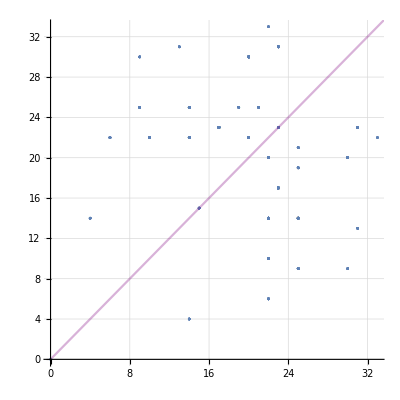

```mathematica
Show[ListPlot[vals345, AspectRatio->1, GridLines->Automatic],Plot[x,{x,0,40}, PlotStyle->Directive[Purple,Opacity[0.3]]]]
```

```mathematica
TableForm[Sort[Tally[Table[Length[RedBlueGreen5[k][[3]]],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]]],TableDepth->2]
```

0 | 2
4 | 10
6 | 15
9 | 40
10 | 30
13 | 10
14 | 130
15 | 12
17 | 60
19 | 20
20 | 120
21 | 15
22 | 170
23 | 150
25 | 125
30 | 70
31 | 40
33 | 5

```mathematica
Table[Labeled[allGraphs5[k,"graph"],Style[k,Red]],{k,Select[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&],Length[RedBlueGreen5[#][[3]]]==33&]}]
```

{-Graphics-28764,-Graphics-27246,-Graphics-22708,-Graphics-9490,-Graphics-364}

```mathematica
7,33,
```